```mathematica
AppendTo[$Path,"/home/lev/Projects/mathematica/FeynArts-3.11"];
Needs["FeynArts`"];
```

SetDelayed::wrsym: Symbol Discard is Protected.

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
L=1;
top=CreateTopologies[L,2->2,Adjacencies->4,ExcludeTopologies->Tadpoles];
quadOnly=Select[top,FreeQ[#,Vertex[Except[4]]]&]

Length[quadOnly]
```

TopologyList[]

0

```mathematica
top;
```

```mathematica
Length[top]
```

74

```mathematica
Length[tops]
```

74

```mathematica
A = Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[4][7]],Propagator[Outgoing][Vertex[1][4],Vertex[4][7]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][6]],Propagator[Loop[1]][Vertex[3][5],Vertex[4][7]],Propagator[Loop[1]][Vertex[3][6],Vertex[4][7]]];
```

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

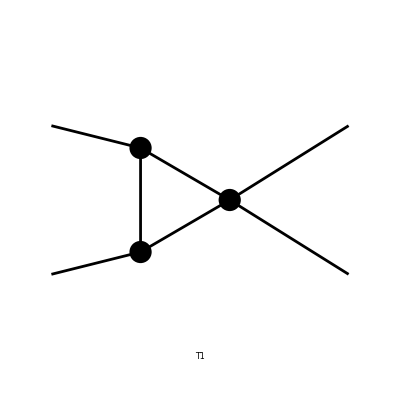

FeynArtsGraphics[2→2][([T1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[A]
```

> Top. 1 aebf/cgdf/egefgf.m, 0 diagrams

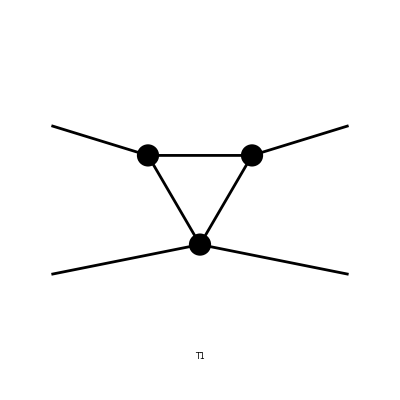

FeynArtsGraphics[2→2][([T1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7]],Propagator[Outgoing][Vertex[1][4],Vertex[4][6]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][7]],Propagator[Loop[1]][Vertex[3][5],Vertex[4][6]],Propagator[Loop[1]][Vertex[3][7],Vertex[4][6]]]]
```

> Top. 1 aebf/cfdf/efee.m, 0 diagrams

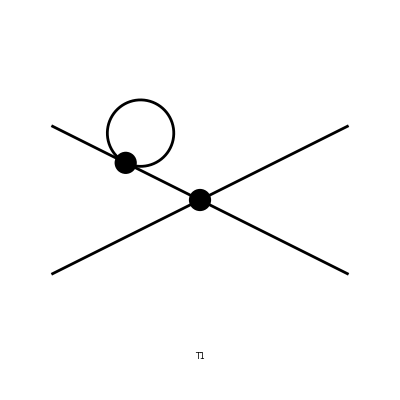

FeynArtsGraphics[2→2][([T1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][6]],Propagator[Outgoing][Vertex[1][3],Vertex[4][6]],Propagator[Outgoing][Vertex[1][4],Vertex[4][6]],Propagator[Internal][Vertex[4][5],Vertex[4][6]],Propagator[Loop[1]][Vertex[4][5],Vertex[4][5]]]]
```